# Reg no: 2017132066

## (1)

```mathematica
Series[Exp[x^4 +x^3 - x^2 ],{x,0,15}]
```

1-x^2+x^3+(3 x^4)/2-x^5-(2 x^6)/3+(3 x^7)/2+(13 x^8)/24-x^9+(3 x^10)/40+(7 x^11)/8-(59 x^12)/720-(17 x^13)/40+(139 x^14)/630+(197 x^15)/720+O[x]^16

## (2)

```mathematica
Roots[x^4+3x^3-3x^2+10==0,x]
```

x==1/2 (-5-√5)||x==1/2 (-5+√5)||x==1-ⅈ||x==1+ⅈ

## (3)

```mathematica
D[(x^3)* ln[x] + cosh[x],{x,3}]
```

6 ln[x]+18 x ln'[x]+9 x^2 ln''[x]+cosh^(3)[x]+x^3 ln^(3)[x]

## (4)

```mathematica
NIntegrate[Sqrt[1-x],{x,0,1}]
```

0.666667

## (5)

```mathematica
MatrixForm[Inverse[({{1,2,3},{4,5,8},{3,2,1}})]]
```

```mathematica
({{-11/8, 1/2, 1/8}, {5/2, -1, 1/2}, {-7/8, 1/2, -3/8}})
```

{{-11/8,1/2,1/8},{5/2,-1,1/2},{-7/8,1/2,-3/8}}

## (6)

{{y→InterpolatingFunction[…]}}

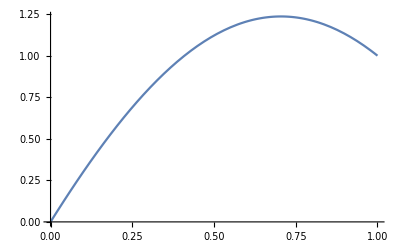

NDSolve::argm: NDSolve called with 2 arguments; 3 or more arguments are expected.

```mathematica
sol =NDSolve[{y''[t]==-Pi^2*(y[t]+1)/4,y[0]==0,y[1]==1},y,{t,0,1}]
Plot[y[t]/.sol,{t,0,1}]
```